```mathematica
k1 :=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\alice_divergenceB N=10 k=1.dat"][[All, {2,1,3}]]
k2 :=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\alice_divergenceB N=10 k=2.dat"][[All, {2,1,3}]]
k11N50:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\old k1,1 N = 50.dat"][[All, {2,1,3}]]
k22N50:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\old k2,2 N = 50.dat"][[All, {2,1,3}]]
k21N50:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000, kappa = 1\\old k2,1 N = 50.dat"][[All, {2,1,3}]]
k1N50var:=Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\High resolution, long equilibration runs\\alice_divergenceB N=50 k=1.dat"][[All, {2,1,3}]]
```

```mathematica
gallaLine := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\stabilityline l0001-001.dat"][[All, {1,2}]]
```

```mathematica
ListDensityPlot[k1, PlotRange->{All, All, All}, InterpolationOrder->0, PlotLegends->All, ColorFunctionScaling -> False,ColorFunction->(ColorData["Rainbow"][(#/3 + 0.8)]&), FrameTicks-> {{All, None},{All, None}},FrameLabel->{{Γ,None},{λ, "k(1,1)"}}, BaseStyle->{FontSize->14} ]
```

$Aborted

```mathematica
ListDensityPlot[k2, PlotRange->{All, All, {-3.2, 1.3}}, InterpolationOrder->0, PlotLegends->None, ColorFunctionScaling->False, ColorFunction->(ColorData["Rainbow"][(#/3 + 0.8)]&),FrameTicks-> {{None, All},{All, None}},FrameLabel->{{None,Γ},{λ, "k(2,2)"}},BaseStyle->{FontSize->14}  ]
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=2 N=10.png", Rasterize[%60], ImageResolution->300]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=1 N=10.png", Rasterize[%63], ImageResolution->300]
```

```mathematica
"D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=2 N=10.png"
```

```mathematica
"D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=1 N=10.png"
```

```mathematica
ListDensityPlot[k1N50, PlotRange->{All, All, All}, InterpolationOrder->0, PlotLegends->Automatic,ColorFunctionScaling->True, ColorFunction->"Rainbow", FrameLabel->{λ, Γ}]
```

ListDensityPlot::arrayerr: k1N50 must be a valid array.

```mathematica
colorf[x_]:= x/4 + 0.4
```

```mathematica
ListDensityPlot[k11N50smooth,PlotRange->{All,All,All},InterpolationOrder->0,PlotLegends->Automatic,ColorFunctionScaling->False, ColorFunction->(ColorData["Rainbow"][(colorf[#])]&),FrameLabel->{λ,Γ}]
```

Import::nffil: File not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListDensityPlot::arrayerr: Symbol[] must be a valid array.

ListDensityPlot[Symbol[],PlotRange→{All,All,All},InterpolationOrder→0,PlotLegends→Automatic,ColorFunctionScaling→False,ColorFunction→(ColorData[Rainbow][colorf[#1]]&),FrameLabel→{λ,Γ}]

```mathematica
Show[%23, ListLinePlot[gallaLine, PlotStyle->Dashed], PlotLabel -> {"k(1,1), N = 50, 15,000 equilibration rounds, 25 samples"}]
```

-Graphics-

```mathematica
ListDensityPlot[k22N50,PlotRange->{All,All,All},InterpolationOrder->0,PlotLegends->Automatic,ColorFunctionScaling->False, ColorFunction->(ColorData["Rainbow"][(colorf[#])]&),FrameLabel->{α,Γ}]
```

-Graphics-

```mathematica
Show[%25, ListLinePlot[gallaLine, PlotStyle->Dashed], PlotLabel -> {"k(2,2), N = 50, 15,000 equilibration rounds, 25 samples"}]
```

-Graphics-

```mathematica
ListDensityPlot[k21N50smooth,PlotRange->{All,All,All},InterpolationOrder->0,PlotLegends->Automatic,ColorFunctionScaling->False, ColorFunction->(ColorData["Rainbow"][(colorf[#])]&),FrameLabel->{λ,Γ}]
```

-Graphics-

```mathematica
Show[%26, ListLinePlot[gallaLine, PlotStyle->Dashed], PlotLabel -> {"k(2,1), N = 50, 15,000 equilibration rounds, 25 samples"}]
```

-Graphics-

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=1,1 N=50.png", Rasterize[%33], ImageResolution->300]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=2,2 N=50.png", Rasterize[%34], ImageResolution->300]
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=2,1 N=50.png", Rasterize[%36], ImageResolution->300]
```

```mathematica
"D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=1,1 N=50.png"
```

```mathematica
"D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=2,2 N=50.png"
```

```mathematica
"D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=2,1 N=50.png"
```

```mathematica
k1LLEs := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\alice_divergenceB N=10 k=1.dat"][[All, 3]]
k11N50LLEs := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000\\k1,1 N = 50.dat"][[All, 3]]
k22N50LLEs := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000\\k2,2 N = 50.dat"][[All, 3]]
k21N50LLEs := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\N = 50, samples = 25, eq rounds = 15000\\k2,1 N = 50.dat"][[All, 3]]
k2LLEs := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\alice_divergenceB N=10 k=2.dat"][[All, 3]]
```

HistogramDistribution::hbins: -- Message text not found -- (0.05)

General::stop: Further output of HistogramDistribution :: hbins will be suppressed during this calculation.

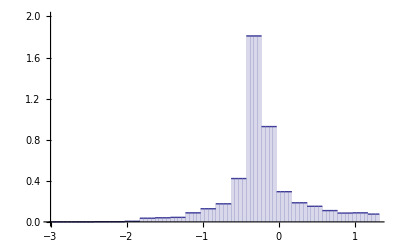

HistogramDistribution::hbins: -- Message text not found -- (0.05)

General::stop: Further output of HistogramDistribution :: hbins will be suppressed during this calculation.

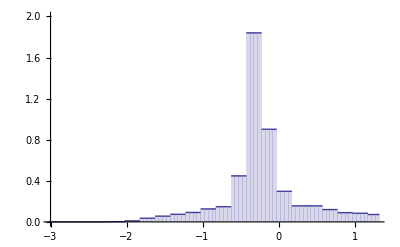

HistogramDistribution::hbins: -- Message text not found -- (0.05)

General::stop: Further output of HistogramDistribution :: hbins will be suppressed during this calculation.

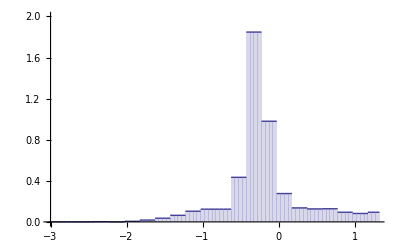

```mathematica
DiscretePlot[PDF[HistogramDistribution[k11N50LLEs, 0.05], x], {x, -3, 1.3}, PlotRange->{0, 2}, ExtentSize->Full]
DiscretePlot[PDF[HistogramDistribution[k21N50LLEs, 0.05], x], {x, -3, 1.3}, PlotRange->{0, 2}, ExtentSize->Full]
DiscretePlot[PDF[HistogramDistribution[k22N50LLEs, 0.05], x], {x, -3, 1.3}, PlotRange->{0, 2}, ExtentSize->Full]
```

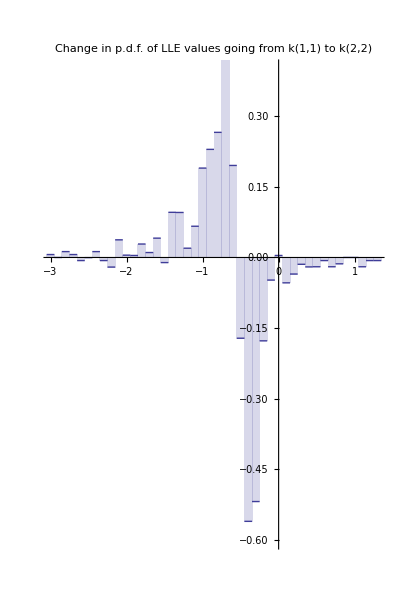

```mathematica
DiscretePlot[{PDF[HistogramDistribution[k2LLEs], x] - PDF[HistogramDistribution[k1LLEs], x]}, {x, -3, 1.3, 0.1},ExtentSize->Full, PlotRange-> {-0.6, 0.4}, AxesOrigin -> {0,0}, BaseStyle->{FontSize->16},PlotRangeClipping->False, PlotLabel->"Change in p.d.f. of LLE values\n going from k(1,1) to k(2,2)\n", AspectRatio->1.5/1,  ImageSize->{Automatic,500} ]
```

```mathematica
Export["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=1 vs k=2 change in distribution.png", Rasterize[%21], ImageResolution->350]
```

```mathematica
"D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\cpp\\k-level reasoning in large games - good version 27-04\\Best results yet\\k=1 vs k=2 change in distribution.png"
```

```mathematica
datak1BL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 BL.dat"][[All, {3,2,4}]]
datak1BR:= Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 BR.dat"][[All, {3,2,4}]]
datak1TL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 TL.dat"][[All, {3,2,4}]]
datak1TR := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k1-1\\alice_varianceB0 TR.dat"][[All, {3,2,4}]]
datak2BL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 BL.dat"][[All, {3,2,4}]]
datak2BR:= Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 BR.dat"][[All, {3,2,4}]]
datak2TL := Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 TL.dat"][[All, {3,2,4}]]
datak2TR:= Import["D:\\Users\\User\\Dropbox\\Dropbox\\MPhys Project\\Processing\\10 samples k2-2\\alice_varianceB0 TR.dat"][[All, {3,2,4}]]
```

```mathematica
datak1B:= Append[Flatten[datak1BL], Flatten[datak1BR]]
datak1T := Append[Flatten[datak1TL], Flatten[datak1TR]]
datak2B:=Append[Flatten[datak2BL], Flatten[datak2BR]]
datak2T:=Append[Flatten[datak2TL], Flatten[datak2TR]]
dataA := Append[datak1B, datak1T]
dataB := Append[datak2B, datak2T]
```

```mathematica
data := Partition[Flatten[dataA], 3]
data2 := Partition[Flatten[dataB], 3]
```

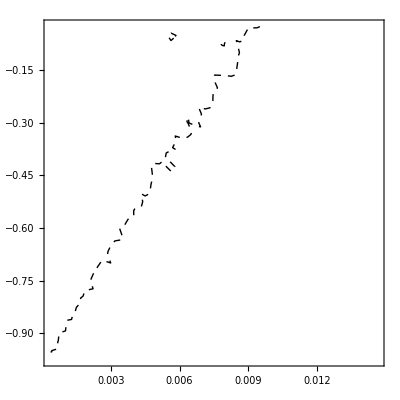

```mathematica
ListContourPlot[data, InterpolationOrder->1, ColorFunction->"SunsetColors", PlotLegends->Automatic, ContourShading -> None, Contours-> {0.001}, ContourStyle->Dashed]
```